```mathematica
(* Import data from Johns Hopkins *)
HopkinsConfirmed = Drop[Import["~/Documents/Wolfram Mathematica/covid19be/johns-hopkins-data/time_series_covid19_confirmed_global.csv",CharacterEncoding->"UTF8"],1];
HopkinsRecovered = Drop[Import["~/Documents/Wolfram Mathematica/covid19be/johns-hopkins-data/time_series_covid19_recovered_global.csv",CharacterEncoding->"UTF8"],1];
HopkinsDeaths = Drop[Import["~/Documents/Wolfram Mathematica/covid19be/johns-hopkins-data/time_series_covid19_deaths_global.csv",CharacterEncoding->"UTF8"],1];
CountryList=AlphabeticSort[DeleteDuplicates[Transpose[HopkinsConfirmed][[2]]]];
```

```mathematica
(* Data for countries can be split over multiple rows in the data from Hopkins *)
DataByCountry = Table[{},{i,1,Length[CountryList]}];
NumberOfDays = Length[Transpose[HopkinsConfirmed]]-4;

For[country = 1, country ≤ Length[CountryList],country++,
TempConfirmed=Table[0,{i,1,NumberOfDays}];
TempRecovered = Table[0,{i,1,NumberOfDays}];
TempDeaths = Table[0,{i,1,NumberOfDays}];
For[row=1,row≤ Length[HopkinsConfirmed],row++,
If[StringMatchQ[CountryList[[country]], HopkinsConfirmed[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempConfirmed = TempConfirmed + Drop[HopkinsConfirmed[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsRecovered],row++,
If[StringMatchQ[CountryList[[country]], HopkinsRecovered[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempRecovered= TempRecovered + Drop[HopkinsRecovered[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsDeaths],row++,
If[StringMatchQ[CountryList[[country]], HopkinsDeaths[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempDeaths = TempDeaths + Drop[HopkinsDeaths[[row]],4];
]
];
TempConfirmedDiff=TempConfirmed-Drop[Join[{0},TempConfirmed],-1];
TempRecoveredDiff=TempRecovered-Drop[Join[{0},TempRecovered],-1];
TempDeathsDiff=TempDeaths-Drop[Join[{0},TempDeaths],-1];
DataByCountry[[country]]= {ToString[CountryList[[country]]],TempConfirmed,TempRecovered,TempDeaths,TempConfirmedDiff,TempRecoveredDiff,TempDeathsDiff};
]
```

```mathematica
(* Model *)
SIR[country_,dday_] := (
n=n0;
i=i0;
r=0;
m=0;
c=r+r+m;
s = n-i-r-m;
cost = 0;
For[sirday=1,sirday≤ dday, sirday++,
lambda = gamma * listr0[[sirday]][[2]];
ds = -lambda i *(s/n);
di = lambda i * (s/n) -gamma i - delta i;
dr = gamma i;
dm = delta i;
dc=di +dr+dm;
s+=ds;
i+=di;
r+=dr;
m+=dm;
c+=dc;
n=s+i+r;
If[sirday≤ Length[DataByCountry[[country]][[2]]],
cost = cost + (c-DataByCountry[[country]][[2]][[sirday]])^2;];
];
Return[{s,i,r,m,c,cost,di}];
);
```

```mathematica
(* Initial values for this country *)
Window =3;
vandaag = Length[DataByCountry[[17]][[2]]];
CFR=DataByCountry[[17]][[4]][[-1]]/DataByCountry[[17]][[2]][[-1]];

n0 = 11400000;
i0=100;
gamma=(1-CFR)/14;
delta = CFR/28;
listr0 = {};
For[day = 1, day <= Length[DataByCountry[[17]][[2]]] + 60, day++,
  listr0 = Join[listr0, {{day, 4.3}}];
  ];
```

```mathematica
(* Fit model to the data *)
For[day=1,day≤Length[DataByCountry[[17]][[2]]]-Window,day++,
bestr0=listr0[[day]][[2]];
bestcost=SIR[17,day+Window][[6]];
For[kr0 = 0.02,kr0≤7,kr0=kr0+0.02,
(* set this possible r0 for all folliwing days and see what the cost is *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] = kr0;];
temp=SIR[17,day + Window];
If[temp[[6]]<bestcost,bestcost=temp[[6]];bestr0=kr0;];
];

(* We found a good r0 for this day, set it for all the following days *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] =bestr0;];
];

(* Generate the lists of data for the plots *)
lists={};
listi={};
listr={};
listm={};
listc={};
listdi={};
For[day=1,day≤Length[DataByCountry[[17]][[2]]]+60,day++,
temp=SIR[17,day];
lists=Append[lists,{day,temp[[1]]}];
listi=Append[listi,{day,temp[[2]]}];
listr=Append[listr,{day,temp[[3]]}];
listm=Append[listm,{day,temp[[4]]}];
listc=Append[listc,{day,temp[[5]]}];
listdi=Append[listdi,{day,temp[[7]]}];
];
```

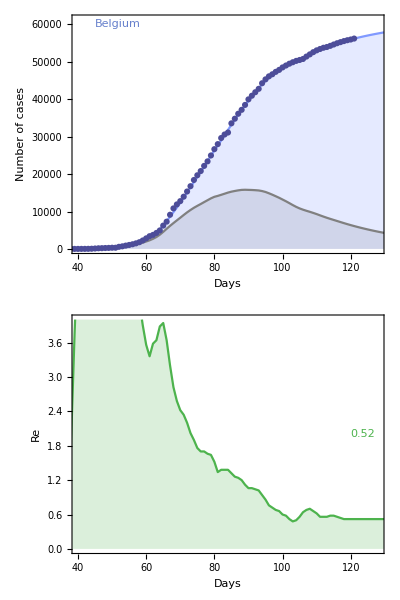

```mathematica
(* Generate plots *)

plotFinalR0 = Graphics[{Text[Style[listr0[[-1]][[2]], Medium,RGBColor[0.3,0.7,0.3]],{120,2},{Left,Center}]}];

plotCountryname = Graphics[{Text[Style[DataByCountry[[17]][[1]], Large,RGBColor[0.4,0.5,0.8]],{45,60000},{Left,Center}]}];

plotModel=Show[{ListPlot[{listi,listc,DataByCountry[[17]][[2]]},PlotRange->{{40,vandaag+7},All},Joined->{True,True,False},Filling->{1-> Bottom,2->Bottom},PlotStyle->{Gray,RGBColor[0.5,0.6,1],RGBColor[0.3,0.3,0.6]},FrameLabel->{"Days","Number of cases"},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thickness[0.002],13],AspectRatio->1/1,ImageSize->600],plotCountryname}];

plotR0=ListPlot[listr0,Joined->True,Filling->{1->Bottom},PlotStyle->RGBColor[0.3,0.7,0.3],FrameLabel->{"Days","Re"},FrameStyle->Directive[Thickness[0.002],13],Frame->True,FrameTicks->Automatic,AspectRatio->1/8,PlotRange->{{40,vandaag+7},{0,4}},ImageSize->600];

ThePlotThickens=Multicolumn[{Show[plotModel,ImagePadding->{{70,10},{20,10}}],Show[{plotR0,plotFinalR0},ImagePadding->{{70,10},{40,5}}]},1]

Export["Desktop/SIR-belgium-22may.pdf", ThePlotThickens, ImageResolution -> 600];
```

```mathematica
N[DataByCountry[[17]][[4]][[-1]]/DataByCountry[[17]][[2]][[-1]]]
DataByCountry[[17]][[4]][[-1]]
```

0.16335

9186